## Harper operator

```mathematica
J[q_, p_] := {{0, 4 π^2 Cos[2 π  p]}, {-4 π^2 Cos[2 π q], 0}}
```

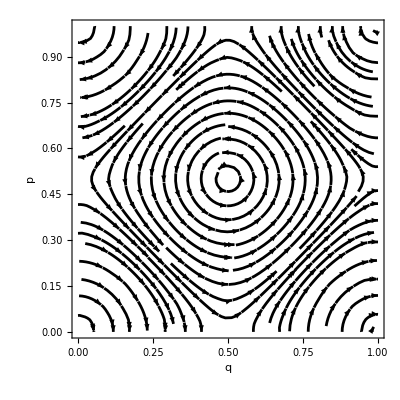

```mathematica
StreamPlot[{2 π Sin[2 π p], -2 π Sin[2 π q]}, {q, 0, 1}, {p, 0, 1}, StreamScale->Automatic, StreamColorFunction->(GrayLevel[0]&), StreamStyle->Thickness[0.005], AxesLabel->{q, p}]
```

```mathematica
A = 1
```

1

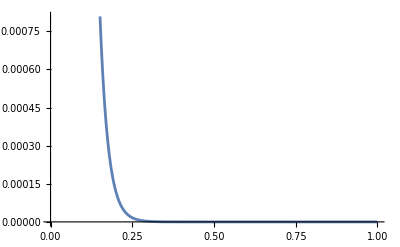

```mathematica
Plot[1/π ArcCot[A Exp[4 π^2 t]],{t, 0, 1}]
```

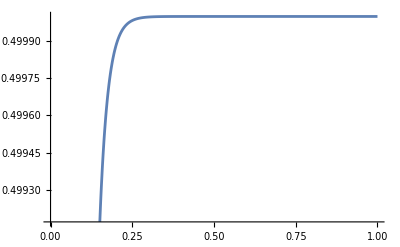

```mathematica
Plot[1/π ArcTan[A Exp[4 π^2 t]],{t, 0, 1}]
```

## Uncertainty of coherent states

```mathematica
Psi[x_,a_]:=1/π^(1/4) Exp[-1/2(x-a)^2]
```

```mathematica
Integrate[Psi[x,a] Psi[x,a],{x, -∞, ∞}]
```

1

```mathematica
Xavg =Integrate[Psi[x,a] x Psi[x, a],{x, -∞, ∞}];
X2avg = Integrate[Psi[x, a] x^2 Psi[x,a],{x, -∞, ∞}];
DelX2 = X2avg - Xavg^2;
DelX = Sqrt[DelX2]
```

1/(√2)

```mathematica
Pavg =Integrate[Psi[x,a] (-I ℏ )D[ Psi[x, a],x],{x, -∞, ∞}];
P2avg = Integrate[Psi[x, a](-ℏ^2) D[Psi[x,a],{x,2}],{x, -∞, ∞}];
DelP2 = P2avg - Pavg^2;
DelP = Sqrt[DelP2]
```

(√(ℏ^2))/(√2)